```mathematica
Import["ToMatlab.m","Package"]
```

# Supporting Information Sec. 3.4 lattice mismatch base on -Graphics-

## AB stacking hexagon Eq. S10

```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions=R>0&&r>0&&as>0&&0≤θ≤π/3&&p∈ Reals&&x∈Reals&&y∈Reals
```

R>0&&r>0&&as>0&&0≤θ≤π/3&&p∈ℝ&&x∈ℝ&&y∈ℝ

```mathematica
fAB[x_,y_,λ_]=Cos[(4 π (x-λ/√3))/(√3 λ)]+2 Cos[(2  π (x-λ/√3))/(√3 λ)] Cos[(2  π y)/λ]
```

2 Cos[(2 π y)/λ] Cos[(2 π (x-λ/(√3)))/(√3 λ)]+Cos[(4 π (x-λ/(√3)))/(√3 λ)]

```mathematica
Plot3D[fAB[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
fAB[x_,y_,λ_]=fAB[x Cos[π/2]-y Sin[π/2],y Cos[π/2]+x Sin[π/2],λ] 
(*Rotate counter-clockwise*)
```

2 Cos[(2 π x)/λ] Cos[(2 π (-y-λ/(√3)))/(√3 λ)]+Cos[(4 π (-y-λ/(√3)))/(√3 λ)]

```mathematica
γ=ArcCos[(Cos[θ]-p)/Sqrt[1+p^2-2p Cos[θ]]]
```

ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]

```mathematica
β=γ-θ;
```

```mathematica
ftheta[x_,y_,λ_,θ_,p_]=fAB[x Cos[-β]-y Sin[-β],y Cos[-β]+x Sin[-β],λ]  (*rotate anticlockwisely by γ-θ *)
```

Cos[(4 π (-λ/(√3)-y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 λ)]+2 Cos[(2 π (-λ/(√3)-y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 λ)] Cos[(2 π (x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/λ]

```mathematica
λ=p Rs/(1+p^2-2 p Cos[θ])^(1/2)
(*λ is distance between AA point*)
```

(p Rs)/(√(1+p^2-2 p Cos[θ]))

```mathematica
f0[x_,y_,Rs_,θ_,p_]=Simplify[ftheta[x,y,λ,θ,p]]
```

2 Cos[(2 π √(1+p^2-2 p Cos[θ]) (x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(p Rs)] Cos[(2 π (√3 p Rs+3 y √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 x √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(3 √3 p Rs)]+Cos[(4 π (√3 p Rs+3 y √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 x √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(3 √3 p Rs)]

```mathematica
nRf0[x_,y_,R_,Rs_,θ_,p_]=f0[x R,y R,Rs,θ,p]
```

2 Cos[(2 π √(1+p^2-2 p Cos[θ]) (R x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-R y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(p Rs)] Cos[(2 π (√3 p Rs+3 R y √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 R x √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(3 √3 p Rs)]+Cos[(4 π (√3 p Rs+3 R y √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 R x √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(3 √3 p Rs)]

```mathematica
nRnasnareauf0[x_,y_,θ_,r_,p_]=Simplify[nRf0[x,y,Rs*p*r,Rs,θ,p]]
```

2 Cos[2 π r √(1+p^2-2 p Cos[θ]) (x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Cos[(2 π (√3+3 r y √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 r x √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(3 √3)]+Cos[(4 π (√3+3 r y √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 r x √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(3 √3)]

```mathematica
hexagonarea=Integrate[Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]
```

(3 √3)/2

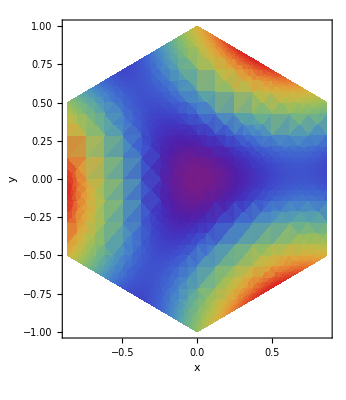

```mathematica
DensityPlot[nRnasnareauf0[x,y,2Degree,4Sqrt[3],0.95],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],AspectRatio->Automatic]
```

```mathematica
t1=AbsoluteTime[];
NEhex[θ_,r_,p_]=Integrate[nRnasnareauf0[x,y,θ,r,p]Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}] ;
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins"]
```

time used 6.265030763 mins

```mathematica
t1=AbsoluteTime[];
ABhex[θ_,r_,p_]=Simplify[NEhex[θ,r,p]/hexagonarea]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins"]
```

(√3 (-1+3 Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]^2) (2 √3 Cos[1/3 π (1+4 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]-√3 Cos[1/3 π (1+2 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+6 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]+2 √3 Sin[1/6 π (1+8 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]-√3 Sin[1/6 π (1+4 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-12 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]-√3 Sin[1/6 π (1+4 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+12 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]-Cos[1/3 π (1+2 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+6 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-4 Cos[π/6+2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]] Sin[(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+Sin[1/6 π (1+4 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-12 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+4 Sin[(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)] Sin[1/3 π (1+6 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-Sin[1/6 π (1+4 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+12 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+Cos[1/3 π (1+2 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-6 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] (-√3+Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])))/(8 π^2 r^2 (1+p^2-2 p Cos[θ]) (-1+2 Cos[2 (θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])]) (-1+√3 Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]) (1+√3 Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))

time used 0.38843008 mins

```mathematica
A1[θ_,p_,r_]:=θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]
```

```mathematica
A2[θ_,p_,r_]:=θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]
```

```mathematica
B1[θ_,p_,r_]:=θ-ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]
B2[θ_,p_,r_]:=θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]
CC[θ_,p_,r_]:=2 √3 r √(1+p^2-2 p Cos[θ])
```

```mathematica
SumABhex[θ_,p_,r_]=√3/(8π^2 r^2(1+p^2-2p Cos[θ])(-1+2Cos[2A1[θ,p,r]]))*(2 √3 Cos[π/3  (1+2CC[θ,p,r] Cos[A1[θ,p,r]])]-√3 Cos[π/3 (1+CC[θ,p,r] Cos[A1[θ,p,r]]+√3 CC[θ,p,r]Sin[A1[θ,p,r]])]+2 √3 Sin[π/6 (1+4CC[θ,p,r]Cos[A1[θ,p,r]])]-√3 Sin[π/6 (1+2CC[θ,p,r]Cos[A1[θ,p,r]]-2 √3 CC[θ,p,r] Sin[A1[θ,p,r]])]-√3 Sin[π/6 (1+2CC[θ,p,r] Cos[A1[θ,p,r]]+2 √3 CC[θ,p,r] Sin[A1[θ,p,r]])]-Cos[π/3 (1+CC[θ,p,r] Cos[A1[θ,p,r] ]+√3 CC[θ,p,r] Sin[A1[θ,p,r] ])]Tan[A1[θ,p,r] ]-4Cos[π/6+π CC[θ,p,r]Sin[A1[θ,p,r] ] /√3]Sin[π CC[θ,p,r] Cos[A1[θ,p,r] ]/3]Tan[A1[θ,p,r] ]+Sin[π/6 (1+2CC[θ,p,r] Cos[A1[θ,p,r]]-2 √3 CC[θ,p,r] Sin[A1[θ,p,r]])]Tan[A1[θ,p,r] ]+4Sin[π CC[θ,p,r] Cos[A1[θ,p,r] ]/3]Sin[π/3 (1+√3 CC[θ,p,r] Sin[A1[θ,p,r] ])]Tan[A1[θ,p,r] ]-Sin[π/6 (1+2CC[θ,p,r] Cos[A1[θ,p,r] ]+2 √3 CC[θ,p,r] Sin[A1[θ,p,r] ])]Tan[A1[θ,p,r] ]+Cos[π/3 (1+CC[θ,p,r] Cos[A1[θ,p,r] ]-√3 CC[θ,p,r] Sin[A1[θ,p,r] ])](-√3+Tan[A1[θ,p,r]]))
```

(√3 (2 √3 Cos[1/3 π (1+4 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]-√3 Cos[1/3 π (1+2 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+6 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]+2 √3 Sin[1/6 π (1+8 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]-√3 Sin[1/6 π (1+4 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-12 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]-√3 Sin[1/6 π (1+4 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+12 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]-Cos[1/3 π (1+2 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+6 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-4 Cos[π/6+2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]] Sin[(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+Sin[1/6 π (1+4 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-12 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+4 Sin[(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)] Sin[1/3 π (1+6 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-Sin[1/6 π (1+4 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+12 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+Cos[1/3 π (1+2 √3 r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-6 r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] (-√3+Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])))/(8 π^2 r^2 (1+p^2-2 p Cos[θ]) (-1+2 Cos[2 (θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])]))